{{x→(-b+√(b^2-4 a c+4 a y))/(2 a)},{x→-(b+√(b^2-4 a c+4 a y))/(2 a)}}

{{x→1/2 (-5-√35)},{x→1/2 (-5+√35)}}

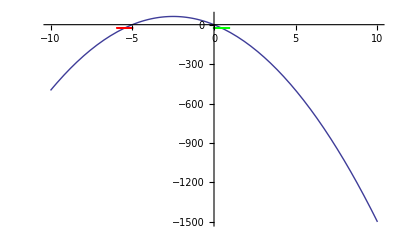

```mathematica
t={a -> -10, b-> -50 ,c->0,y->-25};
para[a_,b_,c_,x_]:=a x^2+b x+c;
solspre=Solve[y==para[a,b,c,x],x]
sols=Solve[y==para[a,b,c,x]/.t,x]
pl={x/.sols[[1]],y/.t};
pr={x/.sols[[2]],y/.t};
Show[
Plot[para[a,b,c,x]/.t,{x,-10,10}],
Graphics[
{
Red,
Circle[pl,0.5],
Green,
Circle[pr,0.5]
}
]
]
```

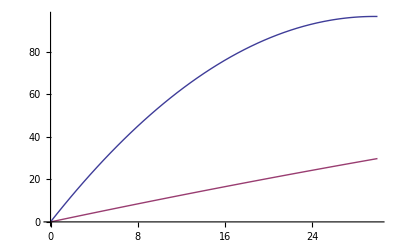

```mathematica
platx=30;
platy=40;
grv=-0.21875;
jmp=6.5;
vx=6;
px[t_]:=platx+vx t;
py[t_]:=grv/2 t^2+t jmp+platy;
f[t_,y_]:=grv/2 t^2+t jmp+y;
(*ParametricPlot[{px[t],py[t]},{t,-10,30}]*)
Plot[{f[t,0],f[t (1/6),0]},{t,0,30}]
```